## Datenimport

```mathematica
rawDataMoodle=Import["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v6\\bombenkalorimeter_gruppe_3_11223.tsv"];
rawDataAuthors=Import["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v6\\bombenkalorimeter_150124.tsv"];
time=Transpose[Drop[rawDataMoodle,1]][[1]];
rawDataMoodleBenzoeacid1=Transpose[Drop[rawDataMoodle,1]][[4]];
rawDataMoodleBenzoeacid2=Transpose[Drop[rawDataMoodle,1]][[5]];
rawDataMoodleBenzoeacid=Transpose[{rawDataMoodleBenzoeacid1, rawDataMoodleBenzoeacid2}];

rawDataMoodleSaccharose1=Transpose[Drop[rawDataAuthors,1]][[2]];
rawDataMoodleSaccharose2=Transpose[Drop[rawDataAuthors,1]][[3]];
rawDataMoodleSaccharose=Transpose[{rawDataMoodleSaccharose1, rawDataMoodleSaccharose2}];
```

```mathematica
meanBenzoeacid=Mean /@ rawDataMoodleBenzoeacid;
sdBenzoeacid=StandardDeviation /@ rawDataMoodleBenzoeacid;

meanSaccharose=Mean /@ rawDataMoodleSaccharose;
sdSaccharose=StandardDeviation /@ rawDataMoodleSaccharose;
```

## Fitting Benzoeacid

FittedModel[20.7308+0.0000534853 x]

20.7308+0.0000534853 x

FittedModel[17.6171+0.00583516 x]

17.6171+0.00583516 x

FittedModel[21.5912+0.000260548 x]

21.5912+0.000260548 x

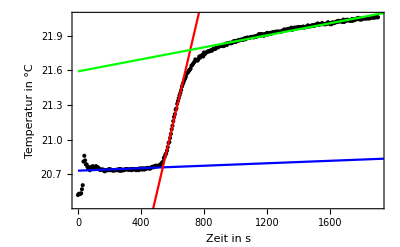

```mathematica
xyPairs=Transpose[{time,meanBenzoeacid}];
xyPairsT1=Take[xyPairs,{20,107}];
linearModelT1=LinearModelFit[xyPairsT1,x,x]
linearFuncT1=linearModelT1["BestFit"]

xyPairsT2=Take[xyPairs,{111,123}];
linearModelT2=LinearModelFit[xyPairsT2,x,x]
linearFuncT2=linearModelT2["BestFit"]

xyPairsT3=Take[xyPairs,{165,382}];
linearModelT3=LinearModelFit[xyPairsT3,x,x]
linearFuncT3=linearModelT3["BestFit"]

(*Visualize the fit*)
Show[ListPlot[xyPairs,PlotStyle->Black],Plot[linearModelT1[x],{x,0,2000},PlotStyle->Blue],Plot[linearModelT2[x],{x,0,2000},PlotStyle->Red],Plot[linearModelT3[x],{x,0,2000},PlotStyle->Green],Frame->True,FrameLabel->{"Zeit in s","Temperatur in °C"}
]
```

## Calc Benzoeacid

```mathematica
sol=Solve[linearFuncT1==linearFuncT2];
interceptT1T2=x/. sol[[1]]
sol=Solve[linearFuncT2==linearFuncT3];
interceptT2T3=x/. sol[[1]]
```

538.536

712.875

```mathematica
A1=-Integrate[linearFuncT1,{x,interceptT1T2,t2}]+Integrate[linearFuncT2,{x,t2,interceptT2T3}];
A2=Integrate[linearFuncT3,{x,interceptT1T2,t2}]-Integrate[linearFuncT2,{x,t2,interceptT2T3}];
sol=Solve[A1==A2,t2]
startTBenzoe=linearModelT1[t2]/.sol[[2]]
mixTBenzoe=linearModelT3[t2]/.sol[[2]]
diffTBenzoe=mixTBenzoe-startTBenzoe
```

{{t2→-6456.82},{t2→482.82}}

21.0755

22.4203

1.34487

```mathematica
hb=-3227.00;
mb=0.458;
Mb=122.121;
Qb=-(mb*hb)/Mb;
Ccal=Qb/diffTBenzoe
```

8.99897

## Fitting Saccharose

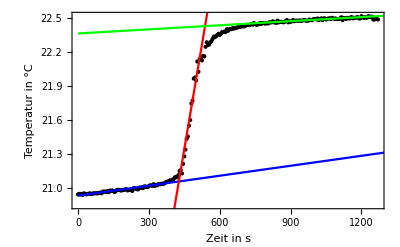

```mathematica
xyPairs=Transpose[{time[[1;;Length[meanSaccharose]]],meanSaccharose}];
xyPairsT1=Take[xyPairs,{10,30}];
linearModelT1=LinearModelFit[xyPairsT1,x,x];
linearFuncT1=linearModelT1["BestFit"];

xyPairsT2=Take[xyPairs,{85,100}];
linearModelT2=LinearModelFit[xyPairsT2,x,x];
linearFuncT2=linearModelT2["BestFit"];

xyPairsT3=Take[xyPairs,{165,200}];
linearModelT3=LinearModelFit[xyPairsT3,x,x];
linearFuncT3=linearModelT3["BestFit"];

(*Visualize the fit*)
Show[ListPlot[xyPairs,PlotStyle->Black],Plot[linearModelT1[x],{x,0,2000},PlotStyle->Blue],Plot[linearModelT2[x],{x,0,2000},PlotStyle->Red],Plot[linearModelT3[x],{x,0,2000},PlotStyle->Green],Frame->True,FrameLabel->{"Zeit in s","Temperatur in °C"}
]
```

## Calc Saccharose

```mathematica
sol=Solve[linearFuncT1==linearFuncT2];
interceptT1T2=x/. sol[[1]]
sol=Solve[linearFuncT2==linearFuncT3];
interceptT2T3=x/. sol[[1]]
```

426.913

537.853

```mathematica
A1=-Integrate[linearFuncT1,{x,interceptT1T2,t2}]+Integrate[linearFuncT2,{x,t2,interceptT2T3}];
A2=Integrate[linearFuncT3,{x,interceptT1T2,t2}]-Integrate[linearFuncT2,{x,t2,interceptT2T3}];
sol=Solve[A1==A2,t2]
startTS=linearModelT1[t2]/.sol[[2]]
mixTS=linearModelT3[t2]/.sol[[2]]
diffTS=mixTBenzoe-startTBenzoe
```

{{t2→-6456.82},{t2→482.82}}

21.0755

22.4203

0.990039

```mathematica
Ms=342.30;
ms=0.433;
hs=-(Ms*diffTS*Ccal)/ms
```

-9567.38